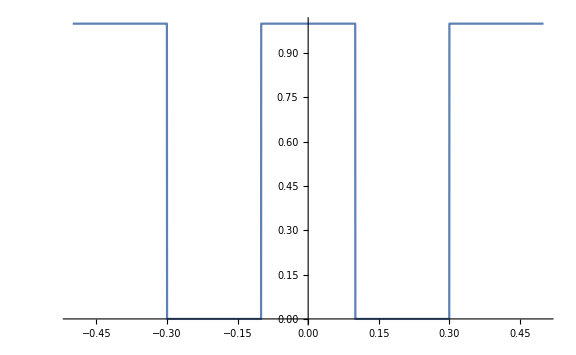

```mathematica
fL = 0.1; fH = 0.3;
fC = (fH+fL)/2;range = fH-fL;
H[f_] := UnitBox[f] - UnitBox[(f-fC)/range] -UnitBox[(-f-fC)/range]
Plot[H[f],{f,-0.5,0.5},ImageSize->Large,Exclusions->None]
```

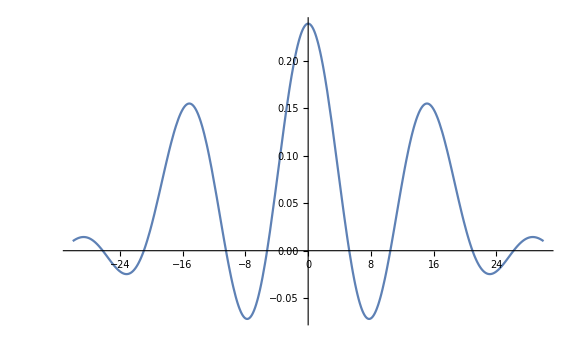

```mathematica
h[t_] :=  InverseFourierTransform[H[f],f,t] (*réponse impulsionnelle*)
Plot[h[t],{t,-30,30},ImageSize->Large,PlotRange->All]
```

```mathematica
M = 64; (*Nombre d'échantillon*)
Hn = Table[H[f],{f,-0.5,0.49,1/M}]
Length[Hn]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1}

64

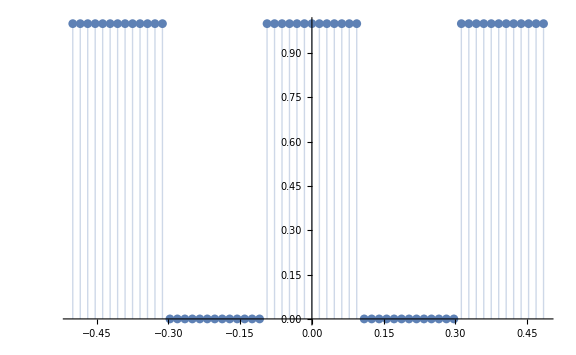

```mathematica
ListPlot[Transpose[{Table[f,{f,-0.5,0.49,1/M}],Hn}],ImageSize->Large,Filling->Axis]
```

```mathematica
hN[k_] :=(1/M)* Sum[Part[Hn,n]*Exp[(I*2*Pi*(n-1 - Floor[M/2] )*k)/M],{n,1,Length[Hn]}]
```

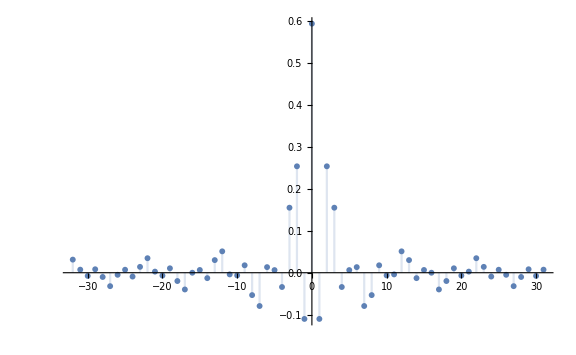

```mathematica
DiscretePlot[hN[k],{k,-(M/2),M/2 - 1,1},ImageSize->Large,PlotRange->All]
```

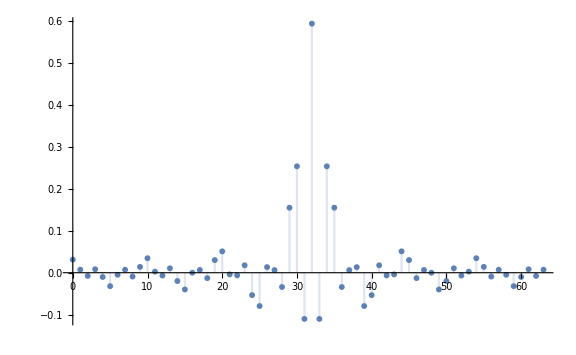

```mathematica
DiscretePlot[hN[k-(M/2 )],{k,0,M-1,1},ImageSize->Large,PlotRange->All]
```

```mathematica
newHN[f_] := Sum[hN[k]*Exp[-I*2Pi*k*f],{k,-(M/2),M/2 - 1}]
```

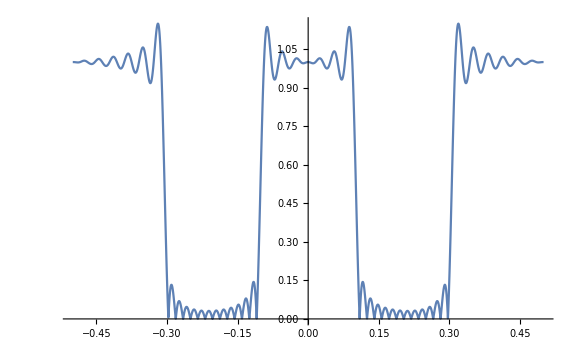

```mathematica
Plot[Abs[newHN[f]],{f,-0.5,0.5},ImageSize->Large]
```